## Leslie-Gower model

### Variables (Trait)

```mathematica
x=.;y=.;
```

### Parameter

#### Parameter (fixed)

```mathematica
b1 = 0;b2 = 0;
(* species 2's trait & the optimum trait *)
x2=-0.1;h1=0;h2 = 0;
(* Coefficients of intraspecific competition of species 1 & 2 *)
alpha1 = 1;alpha2 = 1;
(* Maximum values of fecundity of speices 2 *)
lambdaMax2 = 100;
(* Scaling parameters of competition and fecundity *)
sx1=1;sl1=1;sx2=1;sl2=1;
(* additive genetic variance *)
G=100;
```

#### Parameter (Set values!)

```mathematica
(* Maximum values of coefficients of interspecific competition *)
betaMax=1.1;betaMax1 = betaMax;betaMax2 = betaMax;
(* Maximum values of fecundity of speices 1 *)
lambdaMax1 = 100;
```

### Base equation

```mathematica
f[x_,y_] = lambdaMax1*Exp[-(x-h1)^2/sl1]*(1+(y/(1-y))*betaMax2*Exp[-(x-x2)^2/sx1]) - lambdaMax2*Exp[-(x2-h2)^2/sl1]*((y/(1-y))+betaMax1*Exp[-(x-x2)^2/sx1]);
g[x_,y_]= -G(2 ((alpha1 y) sx1 (-h1+x)+betaMax1 ⅇ^(-(x-x2)^2/sx1)(1-y) (-h1 sx1+sx1 x+sl1 (-x+x2))))/(( (alpha1 y)+betaMax1 ⅇ^(-(x-x2)^2/sx1) (1-y)) sl1 sx1);
```

### Nullicline

#### Plot range

```mathematica
xMin = -0.5;xMax = 1.5;yMin = 0;yMax = 1;
```

#### Plot

>>> Unstable equilibrium & linear stability

{x→0.103113,y→0.50585}

-4046.68

>>> Locally stable equilibrium & linear stability

{x→0.817977,y→0.0547311}

3671.43

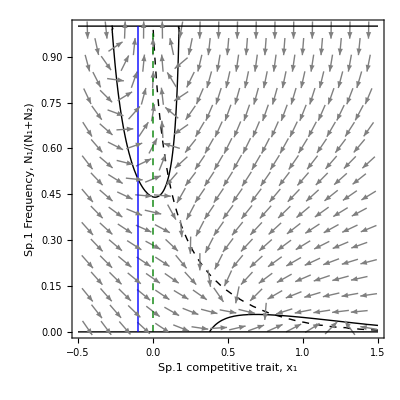

```mathematica
(* contour plot *)
graph2 = ContourPlot[{f[x,y]==0,g[x,y]==0},{x,xMin,xMax},{y,yMin,yMax},ContourShading->None, 
ContourStyle->{{Black,Thick},{Black,Dashed,Thick}},
FrameLabel->{"Sp.1 ecological Trait","Sp.1 Frequency"}];

(* Vector Plot *)
vecP = VectorPlot[ {g[x,y],f[x,y]},{x,xMin,xMax},{y,yMin,yMax},
VectorColorFunction->None, VectorStyle->{Gray}
(*, PlotLegends->Automatic*)] ;

(* calculating equilibrium *)
Print[">>> Unstable equilibrium & linear stability"]
FindRoot[{f[x,y]==0,g[x,y]==0},{{x,0.1},{y,0.5}}] (* {{x,2},{y,0.99}} *)
(* check equilibrium stability *)
a=D[f[x,y],y];
b=D[f[x,y],x];
c=D[g[x,y],y];
d=D[g[x,y],x];
checkStb[x,y]=a*d-b*c;
checkStb[x,y]/.%%%%%%

point1=Graphics[{PointSize[Large],Black,Point[{x,y}]}]/.%%%%%%% ;

Print[">>> Locally stable equilibrium & linear stability"]
FindRoot[{f[x,y]==0,g[x,y]==0},{{x,1.15},{y,0.15}}]
checkStb[x,y]/.%
point2=Graphics[{PointSize[Large],Black,Point[{x,y}]}]/.%%;
l1=Line[{{h1,0},{h1,1}}];(* Line[{{x2,0},{x2,1}}] *)
line1=Graphics[{Thick,Dashed,RGBColor[0,0.5,0],l1}];
l2=Line[{{xMin,0},{xMax,0}}];
line2=Graphics[{Black,l2}];
l3=Line[{{xMin,1},{xMax,1}}];
line3=Graphics[{Black,l3}];
(* fixed species *)
line4=Graphics[{Blue,Thick,Line[{{x2,0},{x2,1}}]}];
line5=Graphics[{Red,Thick,Line[{{0.1,0},{0.1,1}}]}];
(* graph2 *)
Show[graph2, vecP,(* point1,point2, *) line1,line2,line3,line4,(*line5, LPlot,*)
FrameTicksStyle->Directive[AbsoluteThickness[0.5],FontFamily->"Helnetica",FontSize->15],
FrameStyle->Directive[Black]];
Show[graph2, vecP,(* point1,point2, *) line1,line2,line3,line4,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Sp",".1"," ","Frequency"}],","," ",RowBox[{SubscriptBox["N","1"],"/",RowBox[{"(",RowBox[{SubscriptBox["N","1"],"+",SubscriptBox["N","2"]}],")"}]}]}]],None},{RawBoxes[RowBox[{RowBox[{"Sp",".1"," ","competitive"," ","trait"}],","," ",SubscriptBox["x","1"]}]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Helvetica Neue",18,GrayLevel[0]}]
```